# Notes on “Accurate analytic potentials for Li_2 (X^1(Σ^+)_g) and Li_2 (A^1(Σ^+)_u) from 2 to 90 Å, and the radiative lifetime of Li(2p)” from Le Roy et al.

In this paper, Le Roy et al. present a model for the construction of analytic potential energy functions for the two lowest lying singlet states of Li_2, X^1 Σ_g^+ and A^1 Σ_u^+ using a Morse/long-range (MLR) potential function (the basic theory of which is outlined in Sec.III of the paper). This potential energy function is compact, requires relatively few parameters, allows for stable convergence in fits to experimental data, is well-behaved, and its parameters correspond to “key physically interesting properties” such as well depth, equilibrium distance, and long-range potential coefficients.

## The Morse/Long-Range Model for Potential Energy Functions

The basic MLR model for the radial potential energy function has the form,

V_MLR(r) = D_e[1 - (u_LR(r))/(u_LR(r_e))e^(-β(r) y_p(r))]^2

where D_e is the well depth, u_LR(r) is a function which describes the attractive long-range behavior V_LR(r) of the interaction to be,

V_LR(r) = D_e - u_LR(r)

and in general is given by a sum of inverse-power terms,

u_LR(r) = (∑^N)_(i =1)C_m_i/r^m_i= C_m_1/r^m_1+C_m_2/r^m_2+ ... + C_m_N/r^m_N.

The denominator factor in Eq. (1) u_LR(r_e) is the value of the function at the equilibrium length r_e. The radial behavior of u_LR(r) is expressed in terms of the dimensionless radial variable

y_p(r) = y_p^eq(r) =(r^p-r_e^p)/(r^p+r_e^p)

where the superscript “eq” denotes that we are using equilibrium bond length r_e and p is an integer greater than 1 whose value is partly defined (i.e., given a lower bound) by the choice of terms in u_LR(r). The exponent coefficient function β(r) is a slowly varying function of r and is expressed as a polynomial constrained to approach a specified value β_∞ as r →∞,

β(r) = y_p(r) β_∞ + [1 - y_p(r) ](∑^{N_s,N_L})_(i = 0) β_i(y_p(r))^i

where the to upper limits N_s and N_L specify the number of terms required for the sum in short- (r < r_e) and long-range (r > r_e) regions, respectively. By allowing the upper bounds of the summation in Eq.5 to be different in these two region, unphysical behavior, such as potential turnover, is prevent in the short-range region. However, it also means that there is a discontinuities in derivatives of the potential at r = r_e.

The limiting behavior of Eq. (5) (i.e., β_∞) can be using Eq. (1) and Eq. (2),

V_MLR(r) = V(r), for r → ∞

D_e[1 - (u_LR(r))/(u_LR(r_e))e^(-β_∞)]^2 = D_e - u_LR(r)

D_e[1 -(2 e^(-β_∞))/(u_LR(r_e))u_LR(r) + e^(-2 β_∞)/(u_LR(r_e))^2(u_LR(r))^2] = D_e- u_LR(r)

D_e[1 -(2 e^(-β_∞))/(u_LR(r_e))u_LR(r)] ~ D_e- u_LR(r)

(2 D_e e^(-β_∞))/(u_LR(r_e))= 1

β_∞= ln((2 D_e)/(u_LR(r_e)))

Concerning the integer power “p” defining the radial variable of Eq. (4), it must be greater than the difference between the largest and smallest (inverse) powers of the terms included in the definition of u_LR(r) (i.e., p > m_N-m_i). In practice, it is often desirable to set p = m_(N+1)- m_i, where m_(N+1) is the next power predicted by theory that is not included in the chosen definition of u_LR(r), so that the leading contribution of the exponential term in Eq. (1) to the long-range potential u_LR(r) has the same radial behavior as the first missing term, 1/r^(m_(N+1)).

### Extensions of MLR model

##### 1. Addressing a problem associated with m_1= 3 long-range potentials

From Eq. (6), in the limit that r → ∞,  e^(-β_∞)= u_LR(r_e) / (2 D_e) and Eq. (1) thus becomes,

V_MLR(r) ~ D_e - u_LR(r) +(1/(4 D_e)[u_LR(r)])^2.

For a species, such as ground-state Li_2, which dissociates into two S-state atoms, theory tells us that the leading terms contributing to the long-range potential have powers m = 6, 8, 10. In this case, the leading contribution from the quadratic term in Eq. (7) would have an inverse power of 12 and thus, wouldn’t affect the limiting behavior defined by u_LR(r).

However, for a molecular state which dissociated to otherwise identical S- and P- state atoms, the long-range potential would also include a 1/r^3 term. In this case, substituting the two-term definition u_LR(r) = C_3/r^3+ C_6/r^6 into Eq. (7) will yield the long-range behavior,

V_MLR(r) ~ D_e-C_3/r^3-[C_6-(C_3)^2/(4 D_e)]/r^6+ (C_3 C_6/(2 D_e))/r^9+ ((C_6)^2/(4 D_e))/r^12.

The quadratic term introduces both a “fake” contribution to the overall 1/r^6 behavior and unphysical repulsive 1/r^9 and 1/r^12 terms. These problems can be fixed by defining u_LR(r) in a way that corrects for the modification of the effective C_6 value and addition of the 1/r^9 and 1/r^12 terms. If the C_6 coefficient is adjusted as (C^adj)_6= C_6 + (C_3)^2/(4 D_e), the coefficient of the 1/r^6 term in the long-range tail of the MLR potential given by Eq. (8) will be the desired C_6 value. The unphysical 1/r^9 term will disappear if a compensating adjusted 1/r^9 term is included in the definition of u_LR(r) with the coefficient (C^adj)_9= C_3(C^adj)_6/(2 D_e).

Problems due to the quadratic term in Eq. (7) arise when the leading term m_1 is such that second term is equal to m_1^2 or any subsequent terms are equal to sum of two proceeding terms. When these issues occur, the potential must be adjusted accordingly.

##### 2. Extending the definition of β(r) and y_p(r)

```mathematica
ypeq[p_,r_]:= (r^p - 1^p)/(r^p +1^p);
```

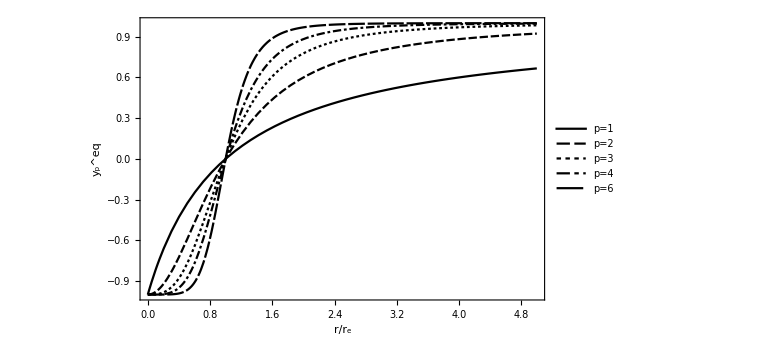

```mathematica
Plot[{ypeq[1,r],ypeq[2,r],ypeq[3,r],ypeq[4,r],ypeq[6,r]},{r,0,5},Frame->True, FrameLabel->{"r/r_e","y_p^eq"},LabelStyle->Large, ImageSize->Large, PlotLegends->{"p=1","p=2","p=3","p=4","p=6"}]
```

A problem associated with the use of y_p^eq(r) as the expansion variable in Eq. (5) is demonstrated by the graph above. With increasing values of p, the expansion variable y_p^eq(r) lies very close to the limiting value of +1 over an increasingly large fraction of the radial range. Over an interval within which y_p^eq(r) changes very little, a relatively high-order polynomial expansion in that variable would be required to provide an accurate description of any function which is not constant there. Mover, except in the highest values of p, y_p^eq(r) still differs significantly from the limiting value of -1 at the lower bound of the region, and thus a polynomial function of the variable could misbehave near this inner region.

One solution to this problem was introducing the use of different polynomial orders in Eq.(5) for the short- (r < r_e) and long-range (r > r_e) regions. However, this solution is not perfect, and introduces its own host of issues. For one as mentioned before there will be discontinuities in the potential at r_e. Moreover, the polynomial coefficients β_i for the smaller order sum usually have magnitudes of order ~ 1, while those of the other are often several orders of magnitude larger than that, and of oscillating sign.

All of these problems can be avoided if we express β(r) in terms of modified radial variable defined relative to a fixed reference distance r_ref>r_e,

y_p(r) = y_p^ref(r) =(r^p-r_ref^p)/(r^p+r_ref^p).

```mathematica
ypref[p_,r_]:= (r^p - 1.5^p)/(r^p +1.5^p);
```

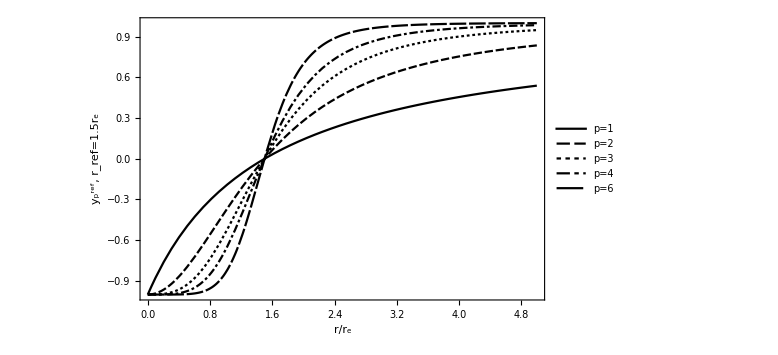

```mathematica
Plot[{ypref[1,r],ypref[2,r],ypref[3,r],ypref[4,r],ypref[6,r]},{r,0,5},Frame->True, FrameLabel->{"r/r_e","y_p^ref, r_ref=1.5r_e"},LabelStyle->Large, ImageSize->Large, PlotLegends->{"p=1","p=2","p=3","p=4","p=6"}]
```

For the case of r_ref=1.5 r_e as depicted in the figure above, the region over which y_p becomes flat and close to the +1 limit is pushed outward to substantially larger r. As a result, for appropriate choices of r_ref, the powers N_s and N_L in Eq. (5) may be set equal to one another (i.e., N_s=N_L), and lower-order polynomials can be used.

However y_p^eq(r) must still be used is the functional form of our MLR potential,

V_MLR(r) = D_e[1 - (u_LR(r))/(u_LR(r_e))e^(-β(r) y_p^eq(r))]^2

because the potential must take on the long-range form

V_MLR(r) ~ D_e - u_LR(r) +(1/(4 D_e)[u_LR(r)])^2

at the equilibrium distance r_e. This no precise method for choosing a value of r_ref but trial-and-error fits using r_ref/r_e~1.1-1.5 will guide one to an optimum choice for r_ref.

In cases in which multiple long-range terms are included in the definition of u_LR(r) (requiring p to be relatively large) and the turning points of the observed levels span a relatively large range of distances, quite high-order exponent polynomials are still required to yield a potential energy able to describe the system accurately. This due to the nature of the radial variable y_p^ref(r), which is still relatively flat at large r for relatively large p. A modification to our definition of the exponential coefficient β(r), given by Eq.(5), addresses this problem.

Examination of the asymptotic behavior of the exponential term in our MLR potential shows that if we introduce a second radial variable  y_q^ref(r) with q≠p, and rewrite β(r) as

β(r) =β_p^q(r) = y_p^ref(r) β_∞ + [1 - y_p^ref(r) ](∑^N)_(i = 0) β_i(y_q^ref(r))^i,

the leading correction to the limiting value (e^(-β_∞)) of the exponential involving the integer q has the form A_(p,q)/r^(p+q). This means that the value of the power q used to define the radial variable in the power series portion of  β_p^q(r)  does not affect the nature of the “leading deviation” from the limiting asymptotic value of the exponential term in Eq. (1) and q, therefore, can be given a relatively small value without causing any distortion of the long-range tail of the potential u_LR(r).

### Potential Energy Functions

For a molecule which dissociates into two S- state atoms, the leading terms in the long-range interaction potential have inverse powers m =6,8,10, and if they are ground-state atoms, the dispersion energy terms are all attractive. Thus, the long-range behavior of the X- state potential may be defined using a two- or three-term version of the function,

u_LR^X(r)  = C_6/r^6+ C_8/r^8+C_10/r^10.

The values for the dispersion coefficient are those of Yan et a. (49). Using the MLR model given by Eq. (9), Eq. (10), and Eq. (11) with a two term long-range potential u_LR^X(r)  = C_6/r^6+ C_8/r^8, p = q = 4, r_ref= 3.5 Å (~1.3 r_e), and N=17, provided Le Roy et al. with a good fit for the ground state X^1 Σ_g^+ (alternatively using q = 3 and N=15, provided an equally good fit).

For a three term long-range potential u_LR^X(r)  = C_6/r^6+ C_8/r^8+C_10/r^10, Le Roy et al. used the following values for the parameters: p = 5, q = 3, and r_ref= 3.85 Å, for their fit. This is their recommended model for the potential energy function of the ground state X^1 Σ_g^+

### Born-Oppenheimer Breakdown Functions

It is necessary to take into account BOB effects that give rise to small differences between the rotationless potentials for different isotopologues, and to the small atomic-mass-dependent contributions to the rotational level energies. The vibration-rotation levels of isotopologue α of diatomic molecule A-B in a given electronic state are the eigenvalues of the radial Schrodinger equation

{-ℏ^2/(2 μ_α) d^2/(d r^2)+ [V_ad^(1)(r) + ΔV_ad^(α)(r)] + (ℏ^2 J(J+1))/(2 μ_α r^2)[1+g^(α)(r)]} ψ_(ν,J)(r) = E_(ν,J) ψ_(ν,J)(r) ,

in which V_ad^(1)(r) is the effective adiabatic interaction potential for a selected reference isotopologue labeled α = 1, ΔV_ad^(α)(r)=V_ad^(α)(r)-V_ad^(1)(r) is the difference between the effective adiabatic potentials for isotopologue α and isotopologue 1, g^(α)(r) is nonadiabatic centrifugal-potential correction function for isotopologue α, and μ_α is the reduced mass defined by the atomic masses M_A^(α) and M_B^(α).  Following established conventions (refs. 31,45,52-54) the BOB terms ΔV_ad^(α)(r) and g^(α)(r) are written as a sum of contributions from the two component atoms Li(A) and Li(B), and which for the present homopolar molecule collapse to,

ΔV_ad^(α)(r) = (((ΔM^(α))_(Li(A)))/((M^(α))_(Li(A)))+((ΔM^(α))_(Li(B)))/((M^(α))_(Li(B)))) S_ad^Li(r),

g^(α)(r) = (((M^(1))_(Li(A)))/((M^(α))_(Li(A)))+((M^(1))_(Li(B)))/((M^(α))_(Li(B))))R_na^Li(r),

where (ΔM^(α))_(Li(A/B))= (M^(α))_(Li(A/B))-(M^(1))_(Li(A/B)) are the difference between the atomic masses of lithium atoms A and B for isotopologue α and isotopologue 1. There is only a single radial strength function of each type S_ad^Li(r) and R_na^Li(r), but two mass factors must be retained in order to describe all three molecular isotopologues. The radial strength functions  S_ad^Li(r) and R_na^Li(r) are expressed as polynomials constrained to have specified asymptotic values just as β(r):

S_ad^Li(r)= y_p_ad^eq(r) (u^Li)_∞ + [1 -  y_p_ad^eq(r) ]∑_(i = 0) (u^Li)_i (y_q_ad^eq(r))^i,

R_na^Li(r)= y_p_na^eq(r) (t^Li)_∞ + [1 -  y_p_na^eq(r) ]∑_(i = 0) (t^Li)_i (y_q_na^eq(r))^i,

in which (u^Li)_∞ and (t^Li)_∞ are the values of these functions in the limit r → ∞, and  (u^Li)_0 and (t^Li)_0 define their values at r=r_e (see ref. 45 for further discussion).  (t^A)_∞= 0.0 for any molecule which dissociates to yield an uncharged atom A, so in our present case,  (t^Li)_∞(X^1 Σ_g^+)=0.0 and Le Roy et al. also adopt the Watson convention for setting the parameter (t^Li)_0=0.0 for the X-state.

Concerning the powers p_(ad,)q_ad,p_na, and q_na, p_ad must be equal to or greater than the power of the longest-range term in the intermolecular potential for the that state. Le Roy et al. set p_ad=q_ad=6 for the X-state and states that it is necessary to specify p_na or q_na for the ground state because their analysis “showed that no centrifugal BOB terms for [this] state could be determined from available data.” Also,  S_ad^Li(r) and R_na^Li(r) are relatively weak and few terms are required to define them and there is no need to introduce an r_ref. Le Roy et al. also define the absolute zero of energy as being the energy of all ground-state atomic isotopes separated at r → ∞, and thus  (u^Li)_∞(X^1 Σ_g^+)=0.0.

ΔV_ad^(α)(r) gives rise to difference between the well depths and equilibrium distances for different Li_2 isotopologues in a given electronic state,

δD_e^(α)=D_e^(α)-D_e^(1)=  (((ΔM^(α))_(Li(A)))/((M^(α))_(Li(A)))+((ΔM^(α))_(Li(B)))/((M^(α))_(Li(B)))) ((u^Li)_∞-(u^Li)_0),

δr_e^(α)=r_e^(α)-r_e^(1)= - (((ΔM^(α))_(Li(A)))/((M^(α))_(Li(A)))+((ΔM^(α))_(Li(B)))/((M^(α))_(Li(B)))) (S'_ad(r_e))/k,

where k is the harmonic force constant at the potential minimum in units cm^-1 Å^-2, and

S'_ad(r_e) = ((d S_ad)/(d r))_(r = r_e)= ((u_∞-u_0) p_ad+ u_1 q_ad)/(2 r_e).

These expressions apply to the description of the X-state.

Values for parameters in MLR potential, energies are given in cm^-1 and lengths are given in Å:

```mathematica
De = 8516.7094;
re = 2.6729932;
C6 = 6.71527 * 10^6;
C8 = 1.12588 * 10^8;
C10 = 2.78604 * 10^9;
p = 5;
q = 3;
rref = 3.85;
βcoefficients = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
```

Parameters in THz and a_0:

```mathematica
c6Hz = C6 * (1.2398*10^-4)*(1.88973)^6*(1/(4.135667696 *10^-15))*(10^-12)
```

9.16786×10^6

```mathematica
c8Hz = C8* (1.2398*10^-4)*(1.88973)^8*(1/(4.135667696 *10^-15))*(10^-12)
```

5.48904×10^8

```mathematica
c10Hz =  C10* (1.2398*10^-4)*(1.88973)^10*(1/(4.135667696 *10^-15))*(10^-12)
```

4.85055×10^10

```mathematica
DeHz =  De* (1.2398*10^-4)*(1/(4.135667696 *10^-15))*(10^-12)
```

255.316

Define V_MLR, u_LR, u_LR(r_e), radial variables y_p^eq, y_p^ref, y_q^ref,  the exponent coefficient function β(r), and its asymptotic limit β_∞

```mathematica
ulr[r_]:=C6/r^6+C8/r^8+C10/r^10;(* c6Hz/r^6+c8Hz/r^8+c10Hz/r^10;*)
```

```mathematica
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
ypeq[r_]:=y[re,r,p];
ypref[r_]:=y[rref,r,p];
yqref[r_]:=y[rref,r,q];
n = Length[βcoefficients];
```

```mathematica
ulre=ulr[re];
```

```mathematica
βinf = Log[(2 De)/ulre](*Log[(2 DeHz)/ulre]*);
```

```mathematica
β[r_]:= βinf ypref[r]+(1-ypref[r])* (βcoefficients[[1]]+Sum[βcoefficients[[j]]*(yqref[r])^j,{j,2,17}]);
```

```mathematica
Vmlr[r_]:= De(1-ulr[r]/ulre*Exp[-β[r]*ypeq[r]])^2-De;(* DeHz(1-ulr[r]/ulre*Exp[-β[r]*ypeq[r]])^2-DeHz;*)
```

MLR potential for X^1 Σ_g^+:

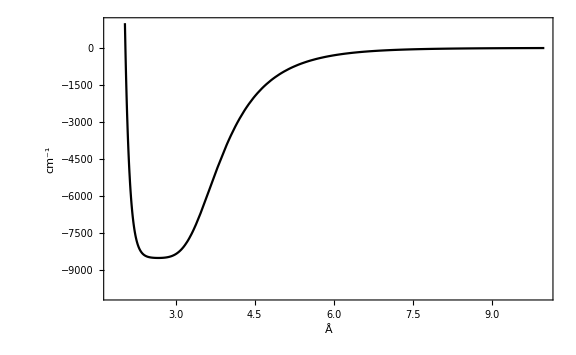

```mathematica
Plot[{Vmlr[r]},{r,1.8,10},Frame->True,ImageSize->Large,FrameLabel->{"Å", "cm^-1"},LabelStyle->Large, PlotRange->{-10000,1000}]
```

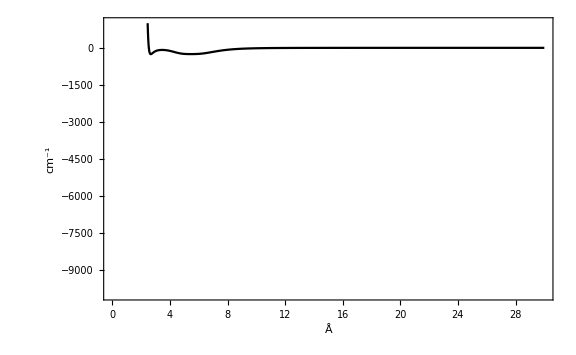

```mathematica
Plot[{Vmlr[r]},{r,1.8,30},Frame->True,ImageSize->Large,FrameLabel->{"Å", "cm^-1"},LabelStyle->Large, PlotRange->{-10000,1000}]
```

a^3(Σ^+)_u Potential:

```mathematica
Detriplet = 333.7587;
retriplet = 4.170053;
c6triplet = 6.67185*10^6;
c8triplet = 1.12629 *10^8;
c10triplet = 2.78683*10^9;
ρLi = 0.54;
rreftriplet = 8.0;
βtripletcoefficients = {-0.51608,-0.09782, 0.1137, -0.0248};
```

```mathematica
DetripletHz = Detriplet* (1.2398*10^-4)*(1/(4.135667696 *10^-15))*(10^-12)
```

10.0055

```mathematica
c6tripletHz = c6triplet * (1.2398*10^-4)*(1.88973)^6*(1/(4.135667696 *10^-15))*(10^-12)
c8tripletHz = c8triplet* (1.2398*10^-4)*(1.88973)^8*(1/(4.135667696 *10^-15))*(10^-12)
c10tripletHz =  c10triplet* (1.2398*10^-4)*(1.88973)^10*(1/(4.135667696 *10^-15))*(10^-12)
```

9.10858×10^6

5.49104×10^8

4.85192×10^10

Addition of Douketis damping function to u_LR(r), (using functional form that is given in Long-range damping functions improve the short-range behavior of ‘MLR’ potential energy functions, Le Roy et. al):

D_m^(ds(s))(r) = (1 - e^((-b^ds(s) (ρ r))/m-(c^ds(s) (ρ r)^2)/m^(1/2)))^(m+s)

```mathematica
Douketis[m_,r_]:= (1 - Exp[-((3.30*ρLi*r)/m)-((0.423*(ρLi r)^2)/m^(1/2))])^(m-1);
D6[r_] := Douketis[6,r];
D8[r_]:= Douketis[8,r];
D10[r_]:=Douketis[10,r];
```

u_LR(r) for a^3(Σ^+)_u :

```mathematica
ulrtriplet[r_]:= D6[r](c6tripletHz/r^6)+D8[r](c8tripletHz/r^8)+D10[r](c10tripletHz/r^10);
```

```mathematica
ulrtripletre = ulrtriplet[retriplet];
```

```mathematica
ypeqtriplet[r_]:=y[retriplet,r,p];
ypreftriplet[r_]:=y[rreftriplet,r,p];
yqreftriplet[r_]:=y[rreftriplet,r,q];
```

```mathematica
βinftriplet = Log[(2 DetripletHz)/ulrtripletre];
```

```mathematica
βtriplet[r_]:= βinftriplet*ypreftriplet[r]+(1-ypreftriplet[r])*(βtripletcoefficients[[1]]+Sum[βtripletcoefficients[[i]]*(yqreftriplet[r])^i,{i,2,Length[βtripletcoefficients]}]);
```

MLR potential for a^3(Σ^+)_u :

```mathematica
MLRtriplet[r_]:= DetripletHz(1-ulrtriplet[r]/ulrtripletre*Exp[-βtriplet[r]*ypeqtriplet[r]])^2-DetripletHz;
```

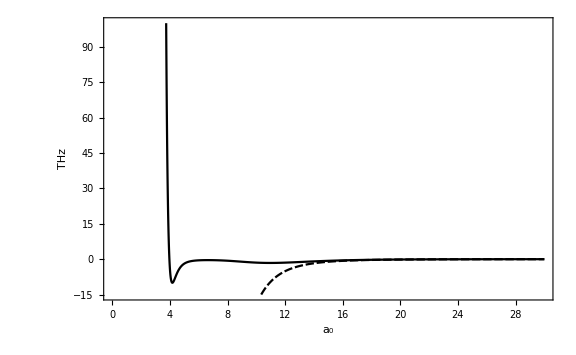

```mathematica
Plot[{MLRtriplet[r],-ulrtriplet[r]},{r,1.5,30},PlotRange->{-15,100},Frame->True,FrameLabel->{"a_0","THz"},LabelStyle->Large,ImageSize->Large]
```

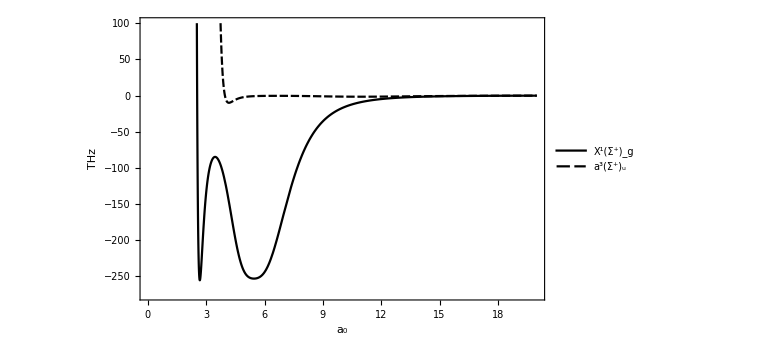

```mathematica
Plot[{Vmlr[r],MLRtriplet[r]},{r,1.8,20},PlotRange->{-275,100},ImageSize->Large, Frame->True, PlotLegends->{"X^1(Σ^+)_g","a^3(Σ^+)_u"},FrameLabel->{"a_0","THz"},LabelStyle->Large]
```

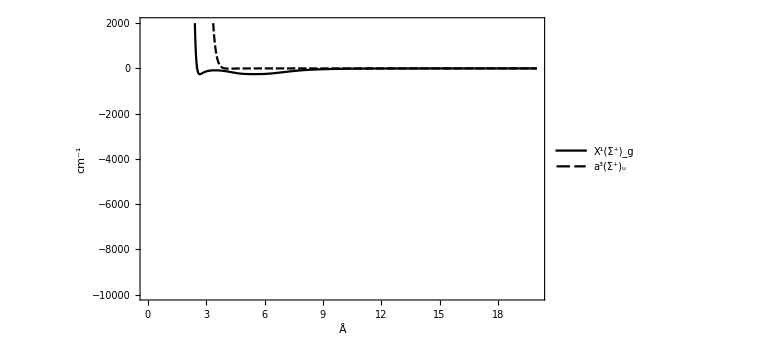

```mathematica
Plot[{Vmlr[r],MLRtriplet[r]},{r,1.8,20},PlotRange->{-10000,2000},ImageSize->Large, Frame->True, PlotLegends->{"X^1(Σ^+)_g","a^3(Σ^+)_u"},FrameLabel->{"Å","cm^-1"},LabelStyle->Large]
```

Singlet with Douketis coefficients:

```mathematica
ulrsinglet2[r_]:= D6[r] c6Hz/r^6+D8[r] c8Hz/r^8+D10[r] c10Hz/r^10;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
ypeq2[r_]:=y[re,r,p];
ypref2[r_]:=y[rref,r,p];
yqref2[r_]:=y[rref,r,q];
β2coefficients = {0.013905144, -1.431068,-1.501106, -0.65906,0.32995, 1.02588,1.2058,1.1927, 3.014,6.568,0.844,-11.24,2.41,26.4,6.3,-23.5, -14.0};
ulrsinglet2re=ulrsinglet2[re];
βinfsinglet2 = Log[(2 DeHz)/ulrsinglet2re];
βsinglet2[r_]:= βinfsinglet2 ypref[r]+(1-ypref[r])*(β2coefficients[[1]]+Sum[β2coefficients[[i]]*(yqref[r])^i,{i,2,n}]);
```

```mathematica
MLRsinglet2[r_]:= DeHz(1-ulrsinglet2[r]/ulrsinglet2re*Exp[-βsinglet2[r]*ypeq[r]])^2-DeHz;
```

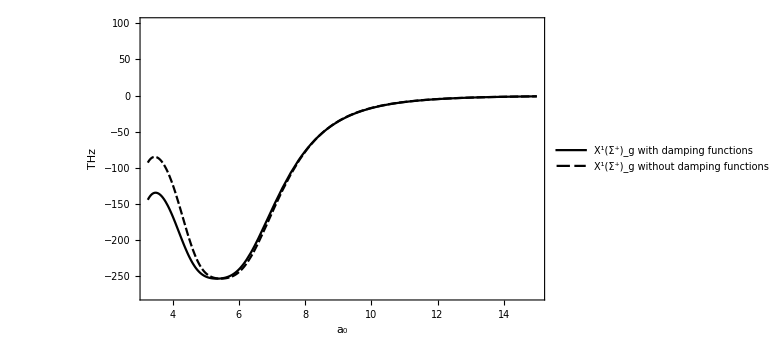

```mathematica
Plot[{MLRsinglet2[r], Vmlr[r]},{r,3.25,15},Frame->True,ImageSize->Large,FrameLabel->{"a_0","THz"},LabelStyle->Large, PlotRange->{-275,100}, Frame->True, PlotLegends->{"X^1(Σ^+)_g with damping functions", "X^1(Σ^+)_g without damping functions"}]
```

Now to construct full radial Hamiltonian with hyperfine and Zeeman interactions with addition of projection operators multiplying the singlet and triplet MLR potentials.

H = -ℏ^2/(2 μ) d^2/(d r^2) + P_0 V_0(r) + P_1 V_1(r) +(l(l+1)ℏ^2)/(2 μ r^2)+ ∑A_i(s_i· i_i) + (g_s^(i) μ_B s_z^(i)+ g_i^(i)μ_N i_z^(i))B

here P_0 and P_1 are the singlet and triplet projection operators, V_0(r) is the potential for the X^1(Σ^+)_g state, V_1(r) is the potential for the a^3(Σ^+)_u state, μ_B is the Bohr magneton, μ_N is the nuclear magneton, B is the magnitude of an external magnetic field, applied along the z-axis, g_s is the electronic gyromagnetic ratio, g_i is the nuclear gyromagnetic ratio, A is the hyperfine constant, s is the electronic spin, i is the nuclear spin, s_z is the component of electronic spin along the z-axis, i_z is the component of the nuclear spin along the z-axis, and the sum is over the two atoms.

Define electronic spin, nuclear spin, hyperfine constant, gyromagnetic ratios for electron and nucleus, nuclear and Bohr magnetons:

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
```

Hyperfine constant in THz:

```mathematica
Li7A = 401.75204335 * 10^-6;
```

Nuclear and Bohr Magnetons in units THz/G:

```mathematica
μb = (9.27*10^-24)/(6.626*10^-34)*10^-12*(1/10^4)
μn = (5.0507837461*10^-27)/(6.626*10^-34)*10^-12*(1/10^4)
```

1.39903×10^-6

7.62267×10^-10

Define hyperfine basis for ^7 Li+^7 Li:

```mathematica
f1m1f2m2basis=Sort[Flatten[Table[Table[{f1,m1, f2, m2},{m1,-f1,f1},{m2,-f2,f2}],{f1,1,2},{f2,1,2}],3]];
```

```mathematica
mF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
```

Singlet and triplet projection operators in hyperfine basis (given in Appendix B of McAlexander Thesis):

1. First expand the hyperfine basis into a linear combination of the molecular basis (i.e. the basis with S = s_1+s_2, I = i_1+i_2, m_S, and m_I as “good” quantum numbers) which are eigenstates of the triplet and singlet operators:

|f_1 m_f_1 f_2 m_f_2⟩ = ∑⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ |S m_s I m_I⟩

where ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ is the Clebsch-Gordan coefficient and is found by the following procedure:

1.a) De-couple |f_1 m_f_1 f_2 m_f_2⟩ basis into the atomic basis (i.e. the basis with m_s_1, m_s_2, m_i_1, and m_i_2 as “good” quantum numbers) through the expression:

|f_1 m_f_1 f_2 m_f_2⟩ = (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2)|s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩

1.b) Re-couple the atomic basis |s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩ to the molecular basis |S m_s I m_I⟩:

|s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩=∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I)|S m_s I m_I⟩

1.c) Use the expressions of (1.a) and (1.b) to express the hyperfine basis  |f_1 m_f_1 f_2 m_f_2⟩ in terms of the molecular basis |S m_s I m_I⟩ :

|f_1 m_f_1 f_2 m_f_2⟩ =(-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) ∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I)|S m_s I m_I⟩

1.d) Take the inner product with |S' m_s'I 'm_I'⟩ to find an expression for ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ :

⟨S' m_s'I 'm_I'|f_1 m_f_1 f_2 m_f_2⟩ = (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) ∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I) ⟨S' m_s'I 'm_I'|S m_s I m_I⟩

= (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) (-1)^(-m_S'-m_I')√((2S'+1)(2I'+1))(s_1 | s_2
m_s_1 | m_s_2 S'
-m_S')(i_1 | i_2
m_i_1 | m_i_2 I'
-m_I')

⟨S' m_s'I 'm_I'|f_1 m_f_1 f_2 m_f_2⟩= ((-1)^(2 i_2-2 s_1-m_1-m_2))^(-m_S'-m_I')√((2 f_1+1)(2 f_2+1)(2S'+1)(2I'+1))∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) (s_1 | s_2
m_s_1 | m_s_2 S'
-m_S')(i_1 | i_2
m_i_1 | m_i_2 I'
-m_I')

2. Using Eq. 23 with the Clebsch-Gordan coefficients given by Eq. 29, determine the matrix elements ⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ for the projection operators in the hyperfine basis:

⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ = ∑_(S,m_S,I,m_I) ∑_(S',m_S',I,'m_I') ⟨S' m_s'I 'm_I'|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ ⟨S' m_s'I 'm_I'| P_(0 or 1)|S m_s I m_I⟩

The projection operator P_(0 or 1) acts on the state |S m_s I m_I⟩ like a delta function where P_0=δ_(S,0) and P_1=δ_(S,1), and thus the matrix elements are:

⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ = ∑_(S,m_S,I,m_I) ∑_(S',m_S',I,'m_I') ⟨S' m_s'I 'm_I'|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ ⟨S' m_s'I 'm_I'| δ_(S, 0 or 1)|S m_s I m_I⟩

= ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 0 or 1)

Construct projection matrices in hyperfine basis:

I. Function to calculate coefficients ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ :

```mathematica
ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];
```

II. Singlet Projection Matrix with elements  ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 0) :

```mathematica
SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[j,3]],mF2basis[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,5},{jp,1,5}];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{1/2,-1/2},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

III. Triplet Projection Matrix with elements  ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 1) :

```mathematica
TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[j,3]],mF2basis[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,5},{jp,1,5}];
```

Hyperfine Interaction:

```mathematica
Hhf[A1_,A2_,f1_,f2_,s1_,i1_,s2_,i2_,ℏ_]:= A1/2 ℏ^2(f1(f1+1)-s1(s1+1)-i1(i1+1)) + A2/2 ℏ^2(f2(f2+1)-s2(s2+1)-i2(i2+1));
HyperfineMatrix = Table[Hhf[Li7A,Li7A,mF2basis[[j,1]],mF2basis[[j,3]],Li7s,Li7i,Li7s,Li7i,1]*KroneckerDelta[j,jp],{j,1,5},{jp,1,5}];
```

Zeeman Interaction:

```mathematica
Hz[f1p_,m1p_,f1_,m1_,f2p_,m2p_,f2_,m2_,gi_,gs_,s_,i_,B_]:= (gs μb B √((2 f1p +1)(2f1 +1)) Sum[ms ThreeJSymbol[{s, ms},{i, mi},{f1p, -m1p}]ThreeJSymbol[{s, ms},{i, mi},{f1, -m1}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m1,m1p]+gi μn B √((2 f1p +1)(2f1 +1)) Sum[mi ThreeJSymbol[{s, ms},{i, mi},{f1p, -m1p}]ThreeJSymbol[{s, ms},{i, mi},{f1, -m1}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m1,m1p])+(gs μb B √((2 f2p +1)(2f2 +1)) Sum[ms ThreeJSymbol[{s, ms},{i, mi},{f2p, -m2p}]ThreeJSymbol[{s, ms},{i, mi},{f2, -m2}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m2,m2p]+gi μn B √((2 f2p +1)(2f2 +1)) Sum[mi ThreeJSymbol[{s, ms},{i, mi},{f2p, -m2p}]ThreeJSymbol[{s, ms},{i, mi},{f2, -m2}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m2,m2p]);
ZeemanMatrix[B_]:= Table[Hz[mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]], Li7gi,Li7gs,Li7s,Li7i,B],{j,1,5},{jp,1,5}];
```

```mathematica
Htest[r_,B_]:= HyperfineMatrix+ZeemanMatrix[B]+TripletProjectionMatrix MLRtriplet[r]+SingletProjectionMatrix Vmlr[r];
```

```mathematica
SingletMatrix2[r_]:= HyperfineMatrix+SingletProjectionMatrix Vmlr[r];
TripletMatrix2[r_]:= HyperfineMatrix+TripletProjectionMatrix Vmlr[r];
```

```mathematica
ListLinePlot[{Table[{j, SingletMatrix2[j][[1,1]]},{j,1,100}],Table[{j, SingletMatrix2[j][[2,2]]},{j,1,100}],Table[{j, SingletMatrix2[j][[3,3]]},{j,1,100}],Table[{j, SingletMatrix2[j][[4,4]]},{j,1,100}],Table[{j, SingletMatrix2[j][[5,5]]},{j,1,100}]},PlotRange->{-0.004,0.004}]
```

-Graphics-

```mathematica
ListLinePlot[{Table[{j, TripletMatrix2[j][[1,1]]},{j,1,100}],Table[{j, TripletMatrix2[j][[2,2]]},{j,1,100}],Table[{j, TripletMatrix2[j][[3,3]]},{j,1,100}],Table[{j, TripletMatrix2[j][[4,4]]},{j,1,100}],Table[{j, TripletMatrix2[j][[5,5]]},{j,1,100}]},PlotRange->{-0.004,0.004}]
```

-Graphics-

```mathematica
ListLinePlot[{Table[{j, Htest[j,0][[1,1]]},{j,1,100}],Table[{j, Htest[j,0][[2,2]]},{j,1,100}],Table[{j, Htest[j,0][[3,3]]},{j,1,100}],Table[{j, Htest[j,0][[4,4]]},{j,1,100}],Table[{j, Htest[j,0][[5,5]]},{j,1,100}]},PlotRange->{-0.004,0.004}]
```

-Graphics-

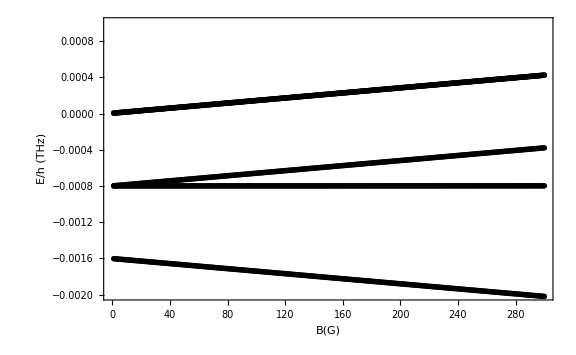

```mathematica
ListLinePlot[{Table[{j, Htest[50,j][[1,1]]},{j,1,300}],Table[{j, Htest[50,j][[2,2]]},{j,1,300}],Table[{j, Htest[50,j][[3,3]]},{j,1,300}],Table[{j, Htest[50,j][[4,4]]},{j,1,300}],Table[{j, Htest[50,j][[5,5]]},{j,1,300}]},PlotRange->{-0.002,0.001},ImageSize->Large,Frame->True,FrameLabel->{"B(G)","E/h (THz)"},LabelStyle->Large]
```

```mathematica
ListLinePlot[{Table[{j, Htest[j,0][[2,1]]},{j,1,100}],Table[{j, Htest[j,0][[2,3]]},{j,1,100}],Table[{j, Htest[j,0][[3,4]]},{j,1,100}],Table[{j, Htest[j,0][[4,5]]},{j,1,100}],Table[{j, Htest[j,0][[3,1]]},{j,1,100}]},PlotRange->{-100,100},ImageSize->Large]
```

-Graphics-

```mathematica
EigenTable = Table[Sort[Eigenvalues[Htest[j,0]]],{j,1,100}];
```

```mathematica
Test1 = Table[{j, EigenTable[[j,1]]},{j,1,100}];
Test2 = Table[{j, EigenTable[[j,2]]},{j,1,100}];
Test3 = Table[{j, EigenTable[[j,3]]},{j,1,100}];
Test4 = Table[{j, EigenTable[[j,4]]},{j,1,100}];
Test5 = Table[{j, EigenTable[[j,5]]},{j,1,100}];
```

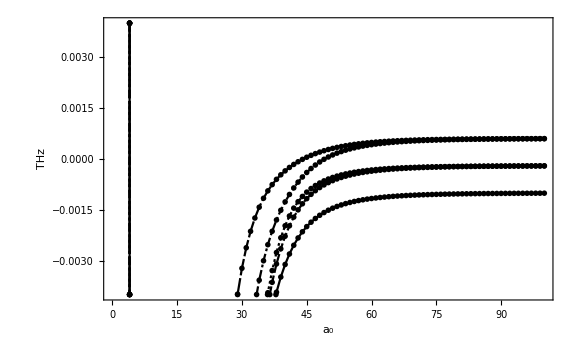

```mathematica
ListLinePlot[{Test1, Test2,Test3,Test4,Test5},ImageSize->Large, PlotRange->{-0.004,0.004},Frame->True,FrameLabel->{"a_0","THz"},LabelStyle->Large]
```

```mathematica
EigenTable2 = Table[Sort[Eigenvalues[Htest[50,j]]],{j,1,300}];
```

```mathematica
Test12 = Table[{j, EigenTable2[[j,1]]},{j,1,300}];
Test22 = Table[{j, EigenTable2[[j,2]]},{j,1,300}];
Test32 = Table[{j, EigenTable2[[j,3]]},{j,1,300}];
Test42 = Table[{j, EigenTable2[[j,4]]},{j,1,300}];
Test52 = Table[{j, EigenTable2[[j,5]]},{j,1,300}];
```

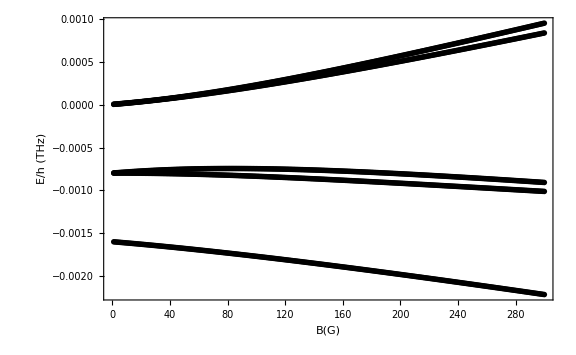

```mathematica
ListLinePlot[{Test12, Test22,Test32,Test42,Test52},ImageSize->Large,Frame->True,FrameLabel->{"B(G)","E/h (THz)"},LabelStyle->Large]
```